0.000231293

0.013857

261.574

980.902

22.9225

750.69

20.0184

0.262

{261.588 Z_1[t]-980.902 Φ_1[t]+Z_1''[t]==0,261.796 Z_2[t]-980.902 Φ_2[t]+Z_2''[t]==0,262.696 Z_3[t]-980.902 Φ_3[t]+Z_3''[t]==0,265.121 Z_4[t]-980.902 Φ_4[t]+Z_4''[t]==0,270.234 Z_5[t]-980.902 Φ_5[t]+Z_5''[t]==0,279.532 Z_6[t]-980.902 Φ_6[t]+Z_6''[t]==0,294.844 Z_7[t]-980.902 Φ_7[t]+Z_7''[t]==0,318.332 Z_8[t]-980.902 Φ_8[t]+Z_8''[t]==0,352.489 Z_9[t]-980.902 Φ_9[t]+Z_9''[t]==0,400.143 Z_10[t]-980.902 Φ_10[t]+Z_10''[t]==0,464.454 Z_11[t]-980.902 Φ_11[t]+Z_11''[t]==0,548.912 Z_12[t]-980.902 Φ_12[t]+Z_12''[t]==0,657.342 Z_13[t]-980.902 Φ_13[t]+Z_13''[t]==0,793.903 Z_14[t]-980.902 Φ_14[t]+Z_14''[t]==0,963.082 Z_15[t]-980.902 Φ_15[t]+Z_15''[t]==0,1169.7 Z_16[t]-980.902 Φ_16[t]+Z_16''[t]==0,1418.92 Z_17[t]-980.902 Φ_17[t]+Z_17''[t]==0,1716.22 Z_18[t]-980.902 Φ_18[t]+Z_18''[t]==0,2067.43 Z_19[t]-980.902 Φ_19[t]+Z_19''[t]==0,2478.69 Z_20[t]-980.902 Φ_20[t]+Z_20''[t]==0}

{-20.0184 Z_1[t]+773.613 Φ_1[t]+Φ_1''[t]==0.000231293 Sin[0.262 t],-20.0184 Z_2[t]+842.38 Φ_2[t]+Φ_2''[t]==0.000231293 Sin[0.524 t],-20.0184 Z_3[t]+956.993 Φ_3[t]+Φ_3''[t]==0.000231293 Sin[0.785 t],-20.0184 Z_4[t]+1117.45 Φ_4[t]+Φ_4''[t]==0.000231293 Sin[1.05 t],-20.0184 Z_5[t]+1323.75 Φ_5[t]+Φ_5''[t]==0.000231293 Sin[1.31 t],-20.0184 Z_6[t]+1575.9 Φ_6[t]+Φ_6''[t]==0.000231293 Sin[1.57 t],-20.0184 Z_7[t]+1873.89 Φ_7[t]+Φ_7''[t]==0.000231293 Sin[1.83 t],-20.0184 Z_8[t]+2217.73 Φ_8[t]+Φ_8''[t]==0.000231293 Sin[2.09 t],-20.0184 Z_9[t]+2607.41 Φ_9[t]+Φ_9''[t]==0.000231293 Sin[2.36 t],-20.0184 Z_10[t]+3042.94 Φ_10[t]+Φ_10''[t]==0.000231293 Sin[2.62 t],-20.0184 Z_11[t]+3524.31 Φ_11[t]+Φ_11''[t]==0.000231293 Sin[2.88 t],-20.0184 Z_12[t]+4051.53 Φ_12[t]+Φ_12''[t]==0.000231293 Sin[3.14 t],-20.0184 Z_13[t]+4624.59 Φ_13[t]+Φ_13''[t]==0.000231293 Sin[3.4 t],-20.0184 Z_14[t]+5243.5 Φ_14[t]+Φ_14''[t]==0.000231293 Sin[3.67 t],-20.0184 Z_15[t]+5908.25 Φ_15[t]+Φ_15''[t]==0.000231293 Sin[3.93 t],-20.0184 Z_16[t]+6618.85 Φ_16[t]+Φ_16''[t]==0.000231293 Sin[4.19 t],-20.0184 Z_17[t]+7375.29 Φ_17[t]+Φ_17''[t]==0.000231293 Sin[4.45 t],-20.0184 Z_18[t]+8177.58 Φ_18[t]+Φ_18''[t]==0.000231293 Sin[4.71 t],-20.0184 Z_19[t]+9025.71 Φ_19[t]+Φ_19''[t]==0.000231293 Sin[4.97 t],-20.0184 Z_20[t]+9919.69 Φ_20[t]+Φ_20''[t]==0.000231293 Sin[5.24 t]}

{{{ⅇ^(-1.9984×10^-15 t) (151+(1.18949×10^-7+4.65472×10^-23 ⅈ) ⅇ^(24 t) Sin[1]^2 Sin[57.1636 t]),ⅇ^(-1.9984×10^-15 t) ((8.29874×10^-25-1.57306×10^-24 ⅈ) ⅇ^1 Cos[15.0249 t]+149)}},18,{{1,1}}}
 |  |  |  |

1
 |  |  |  |

ⅇ^(-1.9984×10^-15 t) ((8.29874×10^-25-1.57306×10^-24 ⅈ) ⅇ^(1.9984×10^-15 t) Cos[15.0249 t]+149) Sin[(π x)/1000]+18+(1) Sin[(π x)/50]
 |  |  |  |

-Graphics3D-

-Graphics3D-

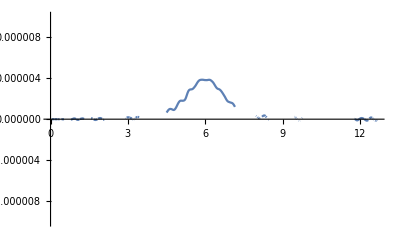

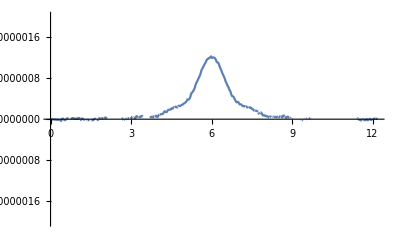

```mathematica
Clear["Global`*"]
F=170000;m0=150000;λ=5;a=7;L=1000;
M=N[2*F*λ/m0/a^2/L]
e=3.45*10^10;d1=15;d2=13;
iy=Pi*d1^4/64*(1-(d2/d1)^2);
c1=e*iy/m0*(Pi/L)^4
ec=1.95*10^11;
dc=0.347;
sc=235;
α=Pi/3;
Ac=Pi*dc^2/4;
ky=2*ec*Ac/sc*Sin[α]^2;
kz=2*ec*Ac/sc*Cos[α]^2;
f1=kz/m0
β=Pi/3;
k1=kz/m0*d1/2*Cos[β]
G=1.38*10^10;
iρ=Pi*d1^4/32*(1-(d2/d1)^2);
g1=G*iρ/m0/a^2*(Pi/L)^2
kφ=kz*(d1/2*Cos[β])^2+ky*(d1/2*Sin[β])^2;
h1=kφ/m0/a^2
j1=kz*(d1/2)*Cos[β]/m0/a^2
V=300;(*km/h*)
v=V*1000/3600;(*m/s*)
v1=N[Pi*v/L,3]
sol1=Table[Subscript[Z, n]''[t]+(n^4*c1+f1)*Subscript[Z, n][t]-k1*Subscript[Φ, n][t]==0,{n,1,20,1}]
sol2=Table[Subscript[Φ, n]''[t]+(n^2*g1+h1)*Subscript[Φ, n][t]-j1*Subscript[Z, n][t]==M*Sin[n*v1*t],{n,1,20,1}]
value=Table[{Subscript[Z, i][t],Subscript[Φ, i][t]}/.DSolve[{sol1[[i]],sol2[[i]],Subscript[Z, i][0]==0,Subscript[Z, i]'[0]==0,Subscript[Φ, i][0]==0,Subscript[Φ, i]'[0]==0},{Subscript[Z, i][t],Subscript[Φ, i][t]},t],{i,1,20,1}]
zandϕ=Sum[value[[n,1]]*Sin[n*Pi/1000*x],{n,1,20,1}];
z=zandϕ[[1]]
ϕ=zandϕ[[2]]
Plot3D[z,{x,0,1000},{t,0,15},PlotRange->{-5*10^-6,5*10^-6}]
Plot3D[ϕ,{x,0,1000},{t,0,15},PlotRange->{-2*10^-6,2*10^-6}]
Plot[z/.x->500,{t,0,13},PlotRange->{-10*10^-6,10*10^-6}]
Plot[ϕ/.x->500,{t,0,13},PlotRange->{-2*10^-6,2*10^-6}]
```